Rect

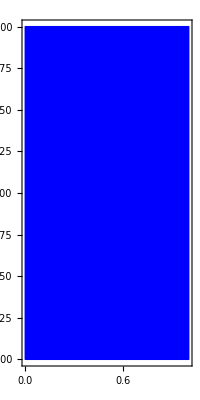

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["gPlotsEx`"];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];

gPrint["Rect"];
Show[pltRect2D[<|"min"->{0,0},"max"->{1,2},
   "colorFunc"->Function[{x,y},Blue]|>],
	ImageSize->Tiny]
```

Rectangle

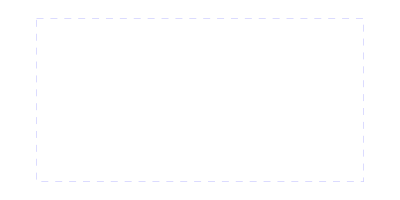

```mathematica
gPrint["Rect Line"];
Show[pltRectLine2D[<|"center"->{0,0},"majorAxis"->{1,0},
	"majorRadius"->1,"minorRadius"->0.5,"color"->Blue,"style"->Dashed|>],
	ImageSize->Tiny]
```

Circle

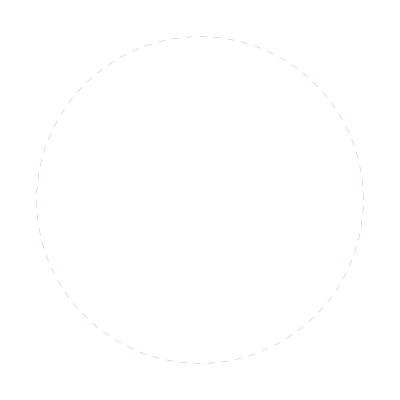

```mathematica
gPrint["Circle"];
Show[pltCircle2D[<|"center"->{0,0},"radius"->1,"color"->Blue,"style"->Dashed|>],
	ImageSize->Tiny]
```